# Notebook for : General Relativity by Straumann

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
October 10, 2021

THIS IS NOT AT ALL OBVIOUS FROM THE TEXT.  IN THE FIRST PART OF THE PROBLEM a is a(t) which is time dependent.  Also e is e(t) and is time dependent.  After an enormous amount of grief one finds the first derivatives on the moments of inertia.  When you go to take the second derivatives you find you need an a dot, e dot, r dot and θ dot.  Two expressions are given for r dot and for θ dot.  What is implied, but not stated is that you now treat both a and e as constants.  I’m embarrassed to admit I don’t know why, and even more embarrassed to admit I’ve spend all god damn day on this.

```mathematica
(* Also See Will Theory and Experiment second edition page 276 for same discussion of binary pulsar coordinate system given on page 337 of Straumann and page 480 of Shapiro and Teukolsky.
Five orbital parameters (ι,Ω,a,e,ω) :
ι inclination angle
Ω called longitude of ascending node 
a semi major axis 
e eccentricity 
ω is the argument of the periastron 
ϕ is called true anamoly  which is called f in Will's test
 *)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book And Related Papers

```mathematica
(* This Edition *) 
Hyperlink["General Relativity Straumann",
"https://www.springer.com/gp/book/9783642060137"]
```

[General Relativity Straumann](https://www.springer.com/gp/book/9783642060137)

```mathematica
Hyperlink["General Relativity Norbert Straumann",
"https://www.springer.com/gp/book/9789400754096"]
```

[General Relativity Norbert Straumann](https://www.springer.com/gp/book/9789400754096)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 15013 Kb

{Utilities`CleanSlate`,VariationalMethods`,GeneralRelativityTensors`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"] (* needed for geodesic equations of metric *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[x]-> dx , 
 Dt[v] -> dv  
};
dtReplace // TableForm
```

Dt[t]→dt
Dt[u]→du
Dt[x]→dx
Dt[v]→dv

## Chapter 4 Calculations

```mathematica
Clear[eq4pt88]
eq4pt88 = 
-dt^2+ dx^2+ L[u]^2( Exp[2β[u]] dy^2+  Exp[-2β[u]] dz^2 )
```

-dt^2+dx^2+(dz^2 ⅇ^(-2 β[u])+dy^2 ⅇ^(2 β[u])) L[u]^2

```mathematica
lineToMetric[ eq4pt88 , {dt,dx,dy,dz} ]  // MatrixForm
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | ⅇ^(2 β[u]) L[u]^2 | 0
0 | 0 | 0 | ⅇ^(-2 β[u]) L[u]^2)

```mathematica
Clear[eq4pt88a]
eq4pt88a = { 
u == (1/(√2))(x-t) , 
v == (1/(√2))(x+t)
} ;
eq4pt88a  // TableForm
```

u==(-t+x)/(√2)
v==(t+x)/(√2)

```mathematica
Flatten[Solve[ eq4pt88a , {x,t} ]] // TableForm
```

x→u/(√2)+v/(√2)
t→1/2 (-√2 u+√2 v)

```mathematica
Dt[  Flatten[Solve[ eq4pt88a , {x,t} ]]]  /. dtReplace  // TableForm
```

dx→du/(√2)+dv/(√2)
dt→1/2 (-√2 du+√2 dv)

```mathematica
eq4pt88  /. ( Dt[  Flatten[Solve[ eq4pt88a , {x,t} ]]]  /. dtReplace  )
```

(du/(√2)+dv/(√2))^2-1/4 (-√2 du+√2 dv)^2+(dz^2 ⅇ^(-2 β[u])+dy^2 ⅇ^(2 β[u])) L[u]^2

```mathematica
eq4pt88  /. ( Dt[  Flatten[Solve[ eq4pt88a , {x,t} ]]]  /. dtReplace  )  // Expand
```

2 du dv+dz^2 ⅇ^(-2 β[u]) L[u]^2+dy^2 ⅇ^(2 β[u]) L[u]^2

```mathematica
Clear[metric4pt88]
metric4pt88 = 
lineToMetric[ ( eq4pt88  /. ( Dt[  Flatten[Solve[ eq4pt88a , {x,t} ]]]  /. dtReplace  )  // Expand  ) , {du,dv,dy,dz} ]  ;
metric4pt88 // MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | ⅇ^(2 β[u]) L[u]^2 | 0
0 | 0 | 0 | ⅇ^(-2 β[u]) L[u]^2)

```mathematica
Clear[eq4pt189a]
eq4pt189a = 
a[t] == -((m1 m2)/(2 ℰ[t]))
```

a[t]==-(m1 m2)/(2 ℰ[t])

```mathematica
Clear[eq4pt189b]
eq4pt189b = 
ℯ[t]^2 == 1 + (2 ℰ[t] L[t]^2 (m1 + m2 ))/(m1^3 m2^3)
```

ℯ[t]^2==1+(2 (m1+m2) L[t]^2 ℰ[t])/(m1^3 m2^3)

```mathematica
Clear[eq4pt190a]
eq4pt190a = 
D[ eq4pt189a , t ]
```

a'[t]==(m1 m2 ℰ'[t])/(2 ℰ[t]^2)

```mathematica
Clear[eq4pt190b]
eq4pt190b = 
D[ eq4pt189b , t ]
```

2 ℯ[t] ℯ'[t]==(4 (m1+m2) L[t] ℰ[t] L'[t])/(m1^3 m2^3)+(2 (m1+m2) L[t]^2 ℰ'[t])/(m1^3 m2^3)

```mathematica
Clear[eq4pt191]
eq4pt191 = {
r[t] ==(a[t](1-ℯ[t]^2))/(1+ℯ[t] Cos[θ[t]]) , 
r1[t] == (m2/(m1+m2))r[t] , 
r2[t] == (m1/(m1+m2))r[t]
} ;
eq4pt191 // TableForm
```

r[t]==(a[t] (1-ℯ[t]^2))/(1+Cos[θ[t]] ℯ[t])
r1[t]==(m2 r[t])/(m1+m2)
r2[t]==(m1 r[t])/(m1+m2)

```mathematica
( eq4pt191[[2]] /. Equal-> Rule  ) 
( eq4pt191[[3]] /. Equal-> Rule  )
```

r1[t]→(m2 r[t])/(m1+m2)

r2[t]→(m1 r[t])/(m1+m2)

```mathematica
Clear[x1]
x1 =(  r1[t] /. ( eq4pt191[[2]] /. Equal-> Rule  )  ) Cos[θ[t]]
```

(m2 Cos[θ[t]] r[t])/(m1+m2)

```mathematica
Clear[x2]
x2 = ( r2[t] /. ( eq4pt191[[3]] /. Equal-> Rule  ) )  Cos[θ[t]]
```

(m1 Cos[θ[t]] r[t])/(m1+m2)

```mathematica
Clear[x]
x = { x1,x2 }
```

{(m2 Cos[θ[t]] r[t])/(m1+m2),(m1 Cos[θ[t]] r[t])/(m1+m2)}

```mathematica
Clear[y1]
y1 =(  r1[t] /. ( eq4pt191[[2]] /. Equal-> Rule  )  ) Sin[θ[t]]
```

(m2 r[t] Sin[θ[t]])/(m1+m2)

```mathematica
Clear[y2]
y2 = ( r2[t] /. ( eq4pt191[[3]] /. Equal-> Rule  ) )  Sin[θ[t]]
```

(m1 r[t] Sin[θ[t]])/(m1+m2)

```mathematica
Clear[y]
y = { y1 , y2 }
```

{(m2 r[t] Sin[θ[t]])/(m1+m2),(m1 r[t] Sin[θ[t]])/(m1+m2)}

```mathematica
Clear[𝓇1]
𝓇1 = {x1,y1}
```

{(m2 Cos[θ[t]] r[t])/(m1+m2),(m2 r[t] Sin[θ[t]])/(m1+m2)}

```mathematica
Clear[𝓇2]
𝓇2 = {x2,y2}
```

{(m1 Cos[θ[t]] r[t])/(m1+m2),(m1 r[t] Sin[θ[t]])/(m1+m2)}

```mathematica
Clear[ℐ]
ℐ = 
Table[ (m1  𝓇1 [[i]] 𝓇1 [[j]]  + m2 𝓇2 [[i]] 𝓇2 [[j]]  )  , {i,1,2}, {j,1,2} ]  // Expand // Simplify   ;
ℐ // MatrixForm
```

((m1 m2 Cos[θ[t]]^2 r[t]^2)/(m1+m2) | (m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]])/(m1+m2)
(m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]])/(m1+m2) | (m1 m2 r[t]^2 Sin[θ[t]]^2)/(m1+m2))

```mathematica
ℐ[[1,1]]
```

(m1 m2 Cos[θ[t]]^2 r[t]^2)/(m1+m2)

```mathematica
Clear[eq4pt193a]
eq4pt193a = 
L[t] == ((m1 m2)/(m1 + m2)) r[t]^2 θ'[t]  ;
```

```mathematica
(* How to solve equation 4pt193 *) 
Flatten[Solve[ ( ( ( Eliminate[ { eq4pt189a,eq4pt189b /.  ( eq4pt193a /. Equal-> Rule  )  }  , ℰ[t] ][[1]]  )  ) //.  ℯ[t]-> √(1-β[t]^2)  ) , θ'[t] ]][[2]]  /. β[t]-> √(1-ℯ[t]^2)
```

θ'[t]→(√(m1+m2) √a[t] √(1-ℯ[t]^2))/r[t]^2

```mathematica
Clear[eq4pt193] (* Clean this up a bit *) 
eq4pt193 = 
θ'[t] ==(( m1 + m2 )^(1/2)√a[t]  (1-ℯ[t]^2)^(1/2))/r[t]^2 ;
( eq4pt193  /. Equal-> Rule )
```

θ'[t]→(√(m1+m2) √a[t] √(1-ℯ[t]^2))/r[t]^2

```mathematica
Clear[eccentricitySimplify]
eccentricitySimplify = { 
ℯ[t]-> √(1-β[t]^2) , 
β[t] -> √(1-ℯ[t]^2) , 
ℯ-> √(1-β^2) , 
β -> √(1-ℯ^2)
} ;
eccentricitySimplify  // TableForm
```

ℯ[t]→√(1-β[t]^2)
β[t]→√(1-ℯ[t]^2)
ℯ→√(1-β^2)
β→√(1-ℯ^2)

```mathematica
(* Could use this for equation 4.193 *) 
( ( Flatten[Solve[ Eliminate[ { eq4pt189a,eq4pt189b } , ℰ[t] ] [[1]]  /. ( eq4pt193a  /. Equal-> Rule )  , θ'[t] ] ][[2]] // Simplify   )  /. eccentricitySimplify[[1]] // PowerExpand   ) /. eccentricitySimplify[[2]]
```

θ'[t]→(√(m1+m2) √a[t] √(1-ℯ[t]^2))/r[t]^2

```mathematica
Flatten[Solve[  ( eq4pt191[[1]]/. ℯ[t]-> ℯ  /. a[t]-> a ) /. Cos[θ[t]]-> β, β]] [[1]] /. β-> Cos[θ[t]]
D[ ( eq4pt191[[1]] /. ℯ[t]-> ℯ  /. a[t]-> a )   , t ] 

D[ ( eq4pt191[[1]] /. ℯ[t]-> ℯ  /. a[t]-> a )   , t ]  /. Flatten[Solve[  ( eq4pt191[[1]]/. ℯ[t]-> ℯ  /. a[t]-> a ) /. Cos[θ[t]]-> β, β]] [[1]] /. β-> Cos[θ[t]] /.( ( eq4pt193 /. ℯ[t]-> ℯ  /. a[t]-> a )  /. Equal-> Rule )  

Clear[eq4pt194a]
eq4pt194a = 
D[ ( eq4pt191[[1]] /. ℯ[t]-> ℯ  /. a[t]-> a )   , t ]  /. Flatten[Solve[  ( eq4pt191[[1]]/. ℯ[t]-> ℯ  /. a[t]-> a ) /. Cos[θ[t]]-> β, β]] [[1]] /. β-> Cos[θ[t]] /.( ( eq4pt193 /. ℯ[t]-> ℯ  /. a[t]-> a )  /. Equal-> Rule )   /. ( eq4pt191[[1]] /. ℯ[t]-> ℯ  /. a[t]-> a  /. Equal-> Rule )
```

Cos[θ[t]]→(a-a ℯ^2-r[t])/(ℯ r[t])

r'[t]==(a ℯ (1-ℯ^2) Sin[θ[t]] θ'[t])/(1+ℯ Cos[θ[t]])^2

r'[t]==(a^(3/2) √(m1+m2) ℯ (1-ℯ^2)^(3/2) Sin[θ[t]])/((1+ℯ Cos[θ[t]])^2 r[t]^2)

r'[t]==(√(m1+m2) ℯ Sin[θ[t]])/(√a √(1-ℯ^2))

```mathematica
(* See above for derivation *) 
Clear[eq4pt194]
eq4pt194 = 
r'[t] ==(ℯ[t] Sin[θ[t]] ( m1 + m2 )^(1/2))/(a[t]^(1/2)(1-ℯ[t]^2)^(1/2))
```

r'[t]==(√(m1+m2) Sin[θ[t]] ℯ[t])/(√a[t] √(1-ℯ[t]^2))

```mathematica
Clear[rDotReplace]
rDotReplace = 
r'[t] -> (ℯ[t] Sin[θ[t]] ( m1 + m2 )^(1/2))/(a[t]^(1/2) (1-ℯ[t]^2)^(1/2))
```

r'[t]→(√(m1+m2) Sin[θ[t]] ℯ[t])/(√a[t] √(1-ℯ[t]^2))

```mathematica
Clear[thetaDotReplace]
thetaDotReplace = 
θ'[t]-> (( m1 + m2 )^(1/2) a[t]^(1/2) (1-ℯ[t]^2)^(1/2))/r[t]^2
```

θ'[t]→(√(m1+m2) √a[t] √(1-ℯ[t]^2))/r[t]^2

```mathematica
Flatten[Solve[ eq4pt191[[1]] , θ[t] ] ][[1]]  /. C[1]-> 0
```

θ[t]→-ArcCos[(a[t]-r[t]-a[t] ℯ[t]^2)/(r[t] ℯ[t])]

```mathematica
Flatten[Solve[ eq4pt191[[1]] , ℯ[t] ] ][[1]]
```

ℯ[t]→(-Cos[θ[t]] r[t]-√(Cos[θ[t]]^2 r[t]^2-4 a[t] (-a[t]+r[t])))/(2 a[t])

```mathematica
Flatten[Solve[ eq4pt191[[1]] , a[t] ] ][[1]]
```

a[t]→-(r[t] (1+Cos[θ[t]] ℯ[t]))/(-1+ℯ[t]^2)

```mathematica
Clear[cosThetaReplace]
cosThetaReplace = 
Collect[ ( Flatten[Solve[ ( eq4pt191[[1]] /. Cos[θ[t]] -> β ) , β ]][[1]]  /. β-> Cos[θ[t] ] ) , a[t] ]
```

Cos[θ[t]]→-1/ℯ[t]+(a[t] (1-ℯ[t]^2))/(r[t] ℯ[t])

```mathematica
Clear[aReplace]
aReplace = 
Flatten[Solve[ eq4pt191[[1]] , a[t] ] ][[1]]
```

a[t]→-(r[t] (1+Cos[θ[t]] ℯ[t]))/(-1+ℯ[t]^2)

```mathematica
Clear[rReplace]
rReplace = 
( eq4pt191[[1]] /. Equal-> Rule  )
```

r[t]→(a[t] (1-ℯ[t]^2))/(1+Cos[θ[t]] ℯ[t])

```mathematica
(* 
For the following calculations see page 496 of Problem Book In Relativity and Gravitation
*)
```

## OverDot[I_xx] Calculation and Reduction ( Find a better way, this works but it’s awkward and tedious )

```mathematica
D[ ℐ[[1,1]] , t ]
```

(2 m1 m2 Cos[θ[t]]^2 r[t] r'[t])/(m1+m2)-(2 m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t])/(m1+m2)

```mathematica
D[ ℐ[[1,1]] , t ]  /. rDotReplace
```

(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))-(2 m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t])/(m1+m2)

```mathematica
D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace
```

(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))-(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]
```

-(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(β[t]^2))/(√(m1+m2))+(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] √(1-β[t]^2))/(√(m1+m2) √a[t] √(β[t]^2))

```mathematica
D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand
```

-(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] β[t])/(√(m1+m2))+(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] √(1-β[t]^2))/(√(m1+m2) √a[t] β[t])

```mathematica
( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]]
```

(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] √(ℯ[t]^2))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))-(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]] // PowerExpand
```

(2 m1 m2 Cos[θ[t]]^2 r[t] Sin[θ[t]] ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))-(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
( ( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify
```

(m1 m2 Sin[2 θ[t]] (Cos[θ[t]] r[t] ℯ[t]+a[t] (-1+ℯ[t]^2)))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
(( ( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify  )
```

(m1 m2 Sin[2 θ[t]] (Cos[θ[t]] r[t] ℯ[t]+a[t] (-1+ℯ[t]^2)))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[IxxDotNumerator]
IxxDotNumerator = Numerator[(( ( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify  ) ]
```

m1 m2 Sin[2 θ[t]] (Cos[θ[t]] r[t] ℯ[t]+a[t] (-1+ℯ[t]^2))

```mathematica
Clear[IxxDotDenominator]
IxxDotDenominator = 
Denominator[(( ( D[ ℐ[[1,1]] , t ]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]  // PowerExpand  ) /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify  ) ]
```

√(m1+m2) √a[t] √(1-ℯ[t]^2)

```mathematica
IxxDotNumerator /. aReplace // Expand // Simplify  // TrigExpand
```

-2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]]

```mathematica
Clear[IxxDot]
IxxDot = 
( IxxDotNumerator /. aReplace // Expand // Simplify  // TrigExpand  )/IxxDotDenominator
```

-(2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[eq4pt195a]
eq4pt195a = 
IxxDot
```

-(2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

## OverDot[I_yy] Calculation and Reduction ( Find a better way, this works but it’s awkward and tedious )

```mathematica
D[ ℐ[[2,2]] , t]
```

(2 m1 m2 r[t] Sin[θ[t]]^2 r'[t])/(m1+m2)+(2 m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t])/(m1+m2)

```mathematica
D[ ℐ[[2,2]] , t]  /. rDotReplace
```

(2 m1 m2 r[t] Sin[θ[t]]^3 ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))+(2 m1 m2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t])/(m1+m2)

```mathematica
D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace
```

(2 m1 m2 r[t] Sin[θ[t]]^3 ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))+(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]]
```

(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(β[t]^2))/(√(m1+m2))+(2 m1 m2 r[t] Sin[θ[t]]^3 √(1-β[t]^2))/(√(m1+m2) √a[t] √(β[t]^2))

```mathematica
D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand
```

(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] β[t])/(√(m1+m2))+(2 m1 m2 r[t] Sin[θ[t]]^3 √(1-β[t]^2))/(√(m1+m2) √a[t] β[t])

```mathematica
( D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand )   /. eccentricitySimplify[[2]]
```

(2 m1 m2 r[t] Sin[θ[t]]^3 √(ℯ[t]^2))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))+(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
( D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand )   /. eccentricitySimplify[[2]] // PowerExpand
```

(2 m1 m2 r[t] Sin[θ[t]]^3 ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))+(2 m1 m2 √a[t] Cos[θ[t]] Sin[θ[t]] √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
( ( D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand )   /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify
```

-(2 m1 m2 (-r[t] Sin[θ[t]]^3 ℯ[t]+a[t] Cos[θ[t]] Sin[θ[t]] (-1+ℯ[t]^2)))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[IyyDotNumerator]
IyyDotNumerator   = 
Numerator[ ( ( D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand )   /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify  ]
```

-2 m1 m2 (-r[t] Sin[θ[t]]^3 ℯ[t]+a[t] Cos[θ[t]] Sin[θ[t]] (-1+ℯ[t]^2))

```mathematica
Clear[IyyDotDenominator]
IyyDotDenominator    = 
Denominator[ ( ( D[ ℐ[[2,2]] , t]  /. rDotReplace /. thetaDotReplace /. eccentricitySimplify[[1]] // PowerExpand )   /. eccentricitySimplify[[2]] // PowerExpand  ) // Simplify  ]
```

√(m1+m2) √a[t] √(1-ℯ[t]^2)

```mathematica
IyyDotNumerator /. aReplace // Expand  // Simplify
```

2 m1 m2 r[t] Sin[θ[t]] (Cos[θ[t]]+ℯ[t])

```mathematica
Clear[IyyDot]
IyyDot = 
( IyyDotNumerator /. aReplace // Expand  // Simplify  )/IyyDotDenominator
```

(2 m1 m2 r[t] Sin[θ[t]] (Cos[θ[t]]+ℯ[t]))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[eq4pt195d]
eq4pt195d = 
IyyDot
```

(2 m1 m2 r[t] Sin[θ[t]] (Cos[θ[t]]+ℯ[t]))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

## OverDot[I_xy] = OverDot[I_yx] Calculation and Reduction ( Find a better way, this works but it’s awkward and tedious )

```mathematica
D[ ℐ[[1,2]] , t ]
```

(2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]] r'[t])/(m1+m2)+(m1 m2 Cos[θ[t]]^2 r[t]^2 θ'[t])/(m1+m2)-(m1 m2 r[t]^2 Sin[θ[t]]^2 θ'[t])/(m1+m2)

```mathematica
D[ ℐ[[1,2]] , t ]  /. thetaDotReplace
```

(m1 m2 √a[t] Cos[θ[t]]^2 √(1-ℯ[t]^2))/(√(m1+m2))-(m1 m2 √a[t] Sin[θ[t]]^2 √(1-ℯ[t]^2))/(√(m1+m2))+(2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]] r'[t])/(m1+m2)

```mathematica
D[ ℐ[[1,2]] , t ]  /. thetaDotReplace /. rDotReplace
```

(2 m1 m2 Cos[θ[t]] r[t] Sin[θ[t]]^2 ℯ[t])/(√(m1+m2) √a[t] √(1-ℯ[t]^2))+(m1 m2 √a[t] Cos[θ[t]]^2 √(1-ℯ[t]^2))/(√(m1+m2))-(m1 m2 √a[t] Sin[θ[t]]^2 √(1-ℯ[t]^2))/(√(m1+m2))

```mathematica
D[ ℐ[[1,2]] , t ]  /. thetaDotReplace /. rDotReplace // Simplify
```

(m1 m2 (r[t] Sin[θ[t]] Sin[2 θ[t]] ℯ[t]-a[t] Cos[2 θ[t]] (-1+ℯ[t]^2)))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[IxyDotNumerator]
IxyDotNumerator = 
Numerator[D[ ℐ[[1,2]] , t ]  /. thetaDotReplace /. rDotReplace // Simplify  ]
```

m1 m2 (r[t] Sin[θ[t]] Sin[2 θ[t]] ℯ[t]-a[t] Cos[2 θ[t]] (-1+ℯ[t]^2))

```mathematica
Clear[IxyDotDenominator]
IxyDotDenominator = 
Denominator[ D[ ℐ[[1,2]] , t ]  /. thetaDotReplace /. rDotReplace // Simplify  ]
```

√(m1+m2) √a[t] √(1-ℯ[t]^2)

```mathematica
Collect[ ( IxyDotNumerator /. aReplace // Expand // Simplify  // TrigExpand  ) ,m1 m2 r[t] ]
```

m1 m2 r[t] (Cos[θ[t]]^2-Sin[θ[t]]^2+Cos[θ[t]] ℯ[t])

```mathematica
Clear[IxyDot]
IxyDot = 
Collect[ ( IxyDotNumerator /. aReplace // Expand // Simplify  // TrigExpand  ) ,m1 m2 r[t] ]/IxyDotDenominator
```

(m1 m2 r[t] (Cos[θ[t]]^2-Sin[θ[t]]^2+Cos[θ[t]] ℯ[t]))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

```mathematica
Clear[eq4pt195g]
eq4pt195g = 
IxyDot
```

(m1 m2 r[t] (Cos[θ[t]]^2-Sin[θ[t]]^2+Cos[θ[t]] ℯ[t]))/(√(m1+m2) √a[t] √(1-ℯ[t]^2))

## I_xx^(..) Calculation and Reduction

```mathematica
Clear[IxxDoubleDot]
IxxDoubleDot = 
( D[( IxxDot /. a[t]-> a  /. ℯ[t]-> ℯ ) , t ] )   /.(  rDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /.(  thetaDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /. ( rReplace/. a[t]-> a  /. ℯ[t]-> ℯ )  // TrigExpand // Simplify
```

(m1 m2 (3 ℯ Cos[θ[t]]+4 Cos[2 θ[t]]+ℯ Cos[3 θ[t]]))/(2 a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IxxDoubleDot  == ( - 2 m1 m2 )/(a(1-ℯ^2))( Cos[2θ[t]] + ℯ  Cos[θ[t]]^3)  // Expand  // Simplify
```

True

## I_yy^(..) Calculation and Reduction

```mathematica
Clear[IyyDoubleDot]
IyyDoubleDot = 
( D[( IyyDot /. a[t]-> a  /. ℯ[t]-> ℯ ) , t ] )   /.(  rDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /.(  thetaDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /. ( rReplace/. a[t]-> a  /. ℯ[t]-> ℯ )  // TrigExpand // Simplify
```

-(m1 m2 (7 ℯ Cos[θ[t]]+4 Cos[2 θ[t]]+ℯ (4 ℯ+Cos[3 θ[t]])))/(2 a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IyyDoubleDot  == (  2 m1 m2 )/(a(1-ℯ^2))( Cos[2θ[t]] +ℯ  Cos[θ[t]]+ ℯ  Cos[θ[t]]^3+ ℯ^2)  // Expand  // Simplify
```

True

## I_xy^(..) Calculation and Reduction

```mathematica
Clear[IxyDoubleDot]
IxyDoubleDot = 
( D[( IxyDot /. a[t]-> a  /. ℯ[t]-> ℯ ) , t ] )   /.(  rDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /.(  thetaDotReplace/. a[t]-> a  /. ℯ[t]-> ℯ )   /. ( rReplace/. a[t]-> a  /. ℯ[t]-> ℯ )  // TrigExpand // Simplify
```

(m1 m2 (4 Cos[θ[t]]+ℯ (3+Cos[2 θ[t]])) Sin[θ[t]])/(a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IxyDoubleDot == ( - 2 m1 m2 )/(a(1-ℯ^2))( Sin[2θ[t]] + ℯ  Sin[θ[t]] + ℯ Sin[θ[t]] Cos[θ[t]]^2) // Expand // Simplify
```

True

## I_xx^(...) Calculation and Reduction

```mathematica
Clear[IxxTripleDot]
IxxTripleDot = 
D[ IxxDoubleDot , t ]   // Simplify
```

-(m1 m2 (4+3 ℯ Cos[θ[t]]) Sin[2 θ[t]] θ'[t])/(a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IxxTripleDot ==  (  2 m1 m2 )/(a(1-ℯ^2))( 2 Sin[2θ[t]] + 3ℯ Cos[θ[t]]^2 Sin[θ[t]] ) θ'[t]  // Simplify
```

True

## I_yy^(...) Calculation and Reduction

```mathematica
Clear[IyyTripleDot]
IyyTripleDot = 
Collect[ D[ IyyDoubleDot , t ] , θ'[t] ]
```

-(m1 m2 (-7 ℯ Sin[θ[t]]-8 Sin[2 θ[t]]-3 ℯ Sin[3 θ[t]]) θ'[t])/(2 a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IyyTripleDot  ==  ( - 2 m1 m2 )/(a(1-ℯ^2))( 2 Sin[2θ[t]] + ℯ Sin[θ[t]] +  3 ℯ Cos[θ[t]]^2 Sin[θ[t]]) θ'[t]  // Simplify
```

True

## I_xy^(...) Calculation and Reduction

```mathematica
Clear[IxyTripleDot]
IxyTripleDot = 
 D[ IxyDoubleDot , t ]   // Together // Simplify
```

(m1 m2 (5 ℯ Cos[θ[t]]+8 Cos[2 θ[t]]+3 ℯ Cos[3 θ[t]]) θ'[t])/(2 a (-1+ℯ^2))

```mathematica
(* my trig expressions look different tho equivalent to the ones given in the text *) 
IxyTripleDot == ( - 2 m1 m2 )/(a(1-ℯ^2))( 2 Cos[2θ[t]] - ℯ Cos[θ[t]] +  3 ℯ Cos[θ[t]]^3) θ'[t]   // Expand  // Simplify
```

True

## I^(...) Calculation and Reduction

```mathematica
Clear[ItripleDot]
ItripleDot = 
IxxTripleDot+IyyTripleDot // Expand  // TrigExpand
```

(2 m1 m2 ℯ Sin[θ[t]] θ'[t])/(a (-1+ℯ^2))

## More Chapter 4 Calculations

```mathematica
(* This just looks different due to factoring double angle identity... expanding it out and collecting gives expression in book as shown below *) 
Clear[Lgw]
Lgw = 
Collect[ (1/5)* ( ( IxxTripleDot^2+ 2*IxyTripleDot^2+IyyTripleDot^2-(1/3)ItripleDot^2 )  // Expand // Simplify  ) // TrigExpand  , θ'[t] ]   // FullSimplify
```

(4 m1^2 m2^2 (24+13 ℯ^2+48 ℯ Cos[θ[t]]+11 ℯ^2 Cos[2 θ[t]]) θ'[t]^2)/(15 a^2 (-1+ℯ^2)^2)

```mathematica
Lgw[[1;;5]]
Lgw[[6]] 
Lgw[[7]]
```

(4 m1^2 m2^2)/(15 a^2 (-1+ℯ^2)^2)

24+13 ℯ^2+48 ℯ Cos[θ[t]]+11 ℯ^2 Cos[2 θ[t]]

θ'[t]^2

```mathematica
Lgw[[6]] == 2*( 12(1+ℯ Cos[θ[t]])^2 + ℯ^2 Sin[θ[t]]^2 )// Expand // Simplify
```

True

```mathematica
Clear[eq4pt196]
eq4pt196 = 
T ==(2 π a^(3/2))/(m1+m2)^(1/2)
```

T==(2 a^(3/2) π)/(√(m1+m2))

```mathematica
Lgw/θ'[t] /. thetaDotReplace /. rReplace /. a[t]-> a  /. ℯ[t]-> ℯ
```

(4 m1^2 m2^2 √(m1+m2) (1+ℯ Cos[θ[t]])^2 (24+13 ℯ^2+48 ℯ Cos[θ[t]]+11 ℯ^2 Cos[2 θ[t]]))/(15 a^(7/2) (1-ℯ^2)^(3/2) (-1+ℯ^2)^2)

```mathematica
Integrate[ ( Lgw/θ'[t] /. thetaDotReplace /. rReplace /. a[t]-> a  /. ℯ[t]-> ℯ  /. θ[t]-> θ  ) , {θ,0,2π}]
```

(2 m1^2 m2^2 √(m1+m2) π (96+292 ℯ^2+37 ℯ^4))/(15 a^(7/2) (1-ℯ^2)^(7/2))

```mathematica
Clear[eq4pt197] (* Factoring out 96 as in the next line will give the form in the book *) 
eq4pt197 = 
( (1/T) /. ( eq4pt196  /. Equal-> Rule )  )* Integrate[ ( Lgw/θ'[t] /. thetaDotReplace /. rReplace /. a[t]-> a  /. ℯ[t]-> ℯ  /. θ[t]-> θ ) , {θ,0,2π}]
```

(m1^2 m2^2 (m1+m2) (96+292 ℯ^2+37 ℯ^4))/(15 a^5 (1-ℯ^2)^(7/2))

```mathematica
( 96+292 ℯ^2+37 ℯ^4 ) / 96  // Expand
```

1+(73 ℯ^2)/24+(37 ℯ^4)/96

```mathematica
Clear[LgwAveraged]
LgwAveraged = 
eq4pt197
```

(m1^2 m2^2 (m1+m2) (96+292 ℯ^2+37 ℯ^4))/(15 a^5 (1-ℯ^2)^(7/2))

```mathematica
Flatten[Solve[ eq4pt189a , ℰ[t]]][[1]]
eq4pt190a
```

ℰ[t]→-(m1 m2)/(2 a[t])

a'[t]==(m1 m2 ℰ'[t])/(2 ℰ[t]^2)

```mathematica
eq4pt190a /. Flatten[Solve[ eq4pt189a , ℰ[t]]][[1]]
```

a'[t]==(2 a[t]^2 ℰ'[t])/(m1 m2)

```mathematica
(* factoring out a 96 will give their exact expression *) 
Clear[eq4pt198]
eq4pt198 = 
( eq4pt190a /. Flatten[Solve[ eq4pt189a , ℰ[t]]][[1]] ) /. ℰ'[t] -> (-LgwAveraged )  /. a[t]-> a
```

a'[t]==-(2 m1 m2 (m1+m2) (96+292 ℯ^2+37 ℯ^4))/(15 a^3 (1-ℯ^2)^(7/2))

```mathematica
( eq4pt196 /. T-> T[t] /. a-> a[t]  ) 
( eq4pt196 /. T-> T[t] /. a-> a[t]  )[[2]]
```

T[t]==(2 π a[t]^(3/2))/(√(m1+m2))

(2 π a[t]^(3/2))/(√(m1+m2))

```mathematica
D[ ( eq4pt196 /. T-> T[t] /. a-> a[t]  )  , t ] 
D[ ( eq4pt196 /. T-> T[t] /. a-> a[t]  )  , t ] [[2]]
```

T'[t]==(3 π √a[t] a'[t])/(√(m1+m2))

(3 π √a[t] a'[t])/(√(m1+m2))

```mathematica
(D[ ( eq4pt196 /. T-> T[t] /. a-> a[t]  )  , t ] [[2]])/(( eq4pt196 /. T-> T[t] /. a-> a[t]  )[[2]])
```

(3 a'[t])/(2 a[t])

```mathematica
Clear[eq4pt199]
eq4pt199 = 
(3/2)eq4pt198[[2]]/a
```

-(m1 m2 (m1+m2) (96+292 ℯ^2+37 ℯ^4))/(5 a^4 (1-ℯ^2)^(7/2))

```mathematica
( Numerator[eq4pt199][[5]] / 96  // Expand  )
```

1+(73 ℯ^2)/24+(37 ℯ^4)/96

```mathematica
Denominator[eq4pt199][[3]]
```

(1-ℯ^2)^(7/2)

```mathematica
Clear[eq4pt200]
eq4pt200 = 
f[ℯ] == ( Numerator[eq4pt199][[5]] / 96  // Expand  )/(Denominator[eq4pt199][[3]])
```

f[ℯ]==(1+(73 ℯ^2)/24+(37 ℯ^4)/96)/((1-ℯ^2)^(7/2))

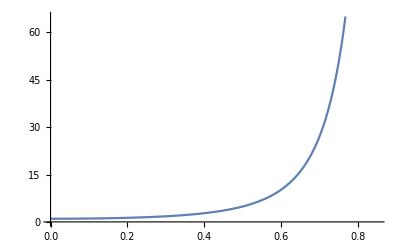

```mathematica
Plot[ eq4pt200[[2]] , {ℯ,0,0.85} ]
```

```mathematica
Clear[eq4pt201a]
eq4pt201a = { 
 m == m1 + m2 , 
η == (m1 m2)/(m1+m2)^2 , 
ℳ == η^(5/3) m 
} ;
```

```mathematica
eq4pt201a[[1]] /. Equal-> Rule 
eq4pt201a[[2]] /. Equal-> Rule
```

m→m1+m2

η→(m1 m2)/(m1+m2)^2

```mathematica
eq4pt201a[[3]] 
eq4pt201a[[3]] /. ( eq4pt201a[[1]] /. Equal-> Rule  ) /. ( eq4pt201a[[2]] /. Equal-> Rule  )  // PowerExpand // Simplify
```

ℳ==m η^(5/3)

ℳ==(m1^(5/3) m2^(5/3))/(m1+m2)^(7/3)

## Chapter 5

```mathematica
Clear[eq5pt184]
eq5pt184 = 
K == { Cos[Ω] , Sin[Ω] , 0 }
```

K=={Cos[Ω],Sin[Ω],0}

```mathematica
Clear[eq5pt185]
eq5pt185 = 
𝒩 == {  Sin[ι]  Sin[Ω] ,- Sin[ι]  Cos[Ω],Cos[ι] }
```

𝒩=={Sin[ι] Sin[Ω],-Cos[Ω] Sin[ι],Cos[ι]}

```mathematica
θ == ω+ϕ
```

θ==ϕ+ω

```mathematica
Flatten[ Solve[ θ == ω+ϕ , ϕ] ][[1]]
```

ϕ→θ-ω

```mathematica
Cos[(ω+ϕ)]( K /.(  eq5pt184  /. Equal-> Rule )  )
```

{Cos[ϕ+ω] Cos[Ω],Cos[ϕ+ω] Sin[Ω],0}

```mathematica
Sin[(ω+ϕ)]Cross[ ( 𝒩 /. ( eq5pt185  /. Equal-> Rule ) ) , (  K /.(  eq5pt184  /. Equal-> Rule )  ) ]
```

{-Cos[ι] Sin[ϕ+ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[ϕ+ω],Sin[ϕ+ω] (Cos[Ω]^2 Sin[ι]+Sin[ι] Sin[Ω]^2)}

```mathematica
Clear[eq5pt186]
eq5pt186 = 
Cos[(ω+ϕ)]( K /.(  eq5pt184  /. Equal-> Rule )  )  + Sin[(ω+ϕ)]Cross[ ( 𝒩 /. ( eq5pt185  /. Equal-> Rule ) ) , (  K /.(  eq5pt184  /. Equal-> Rule )  ) ]
```

{Cos[ϕ+ω] Cos[Ω]-Cos[ι] Sin[ϕ+ω] Sin[Ω],Cos[ι] Cos[Ω] Sin[ϕ+ω]+Cos[ϕ+ω] Sin[Ω],Sin[ϕ+ω] (Cos[Ω]^2 Sin[ι]+Sin[ι] Sin[Ω]^2)}

```mathematica
Clear[eq5pt187]
eq5pt187 = 
x1  == ( r1 * eq5pt186  ) /. Flatten[ Solve[ θ == ω+ϕ , ϕ] ][[1]]  // Expand // Simplify  ;
( eq5pt187  /. Equal-> Rule )
```

(m2 Cos[θ[t]] r[t])/(m1+m2)→{r1 Cos[θ] Cos[Ω]-r1 Cos[ι] Sin[θ] Sin[Ω],r1 Cos[ι] Cos[Ω] Sin[θ]+r1 Cos[θ] Sin[Ω],r1 Sin[θ] Sin[ι]}

```mathematica
Clear[eq5pt188]
eq5pt188 = 
eq5pt187[[3]] /. (  θ == ω+ϕ /. Equal-> Rule )
```

Part::partw: Part 3 of (m2 Cos[θ[t]] r[t])/(m1+m2)=={r1 Cos[θ] Cos[Ω]-r1 Cos[ι] Sin[θ] Sin[Ω],r1 Cos[ι] Cos[Ω] Sin[θ]+r1 Cos[θ] Sin[Ω],r1 Sin[θ] Sin[ι]} does not exist.

Part::partw: Part 3 of (m2 Cos[(ϕ+ω)[t]] r[t])/(m1+m2)=={r1 Cos[ϕ+ω] Cos[Ω]-r1 Cos[ι] Sin[ϕ+ω] Sin[Ω],r1 Cos[ι] Cos[Ω] Sin[ϕ+ω]+r1 Cos[ϕ+ω] Sin[Ω],r1 Sin[ι] Sin[ϕ+ω]} does not exist.

((m2 Cos[(ϕ+ω)[t]] r[t])/(m1+m2)=={r1 Cos[ϕ+ω] Cos[Ω]-r1 Cos[ι] Sin[ϕ+ω] Sin[Ω],r1 Cos[ι] Cos[Ω] Sin[ϕ+ω]+r1 Cos[ϕ+ω] Sin[Ω],r1 Sin[ι] Sin[ϕ+ω]})⟦3⟧

```mathematica
Clear[eq5pt189]
eq5pt189 = 
r1 ==(a1(1-ℯ^2))/(1+ℯ Cos[θ]) ;
( eq5pt189  /. Equal-> Rule  )
```

r1→(a1 (1-ℯ^2))/(1+ℯ Cos[θ])

## Check This

```mathematica
x1 /. ( eq5pt187  /. Equal-> Rule )   /. θ-> ( ω+ϕ)
```

{r1 Cos[ϕ+ω] Cos[Ω]-r1 Cos[ι] Sin[ϕ+ω] Sin[Ω],r1 Cos[ι] Cos[Ω] Sin[ϕ+ω]+r1 Cos[ϕ+ω] Sin[Ω],r1 Sin[ι] Sin[ϕ+ω]}

```mathematica
( eq5pt189  /. Equal-> Rule  )
```

r1→(a1 (1-ℯ^2))/(1+ℯ Cos[θ])

```mathematica
Clear[orbitPath]
orbitPath = 
( x1 /. ( eq5pt187  /. Equal-> Rule )   /. θ-> ( ω+ϕ)   ) /. ( eq5pt189  /. Equal-> Rule  )
```

{(a1 (1-ℯ^2) Cos[ϕ+ω] Cos[Ω])/(1+ℯ Cos[θ])-(a1 (1-ℯ^2) Cos[ι] Sin[ϕ+ω] Sin[Ω])/(1+ℯ Cos[θ]),(a1 (1-ℯ^2) Cos[ι] Cos[Ω] Sin[ϕ+ω])/(1+ℯ Cos[θ])+(a1 (1-ℯ^2) Cos[ϕ+ω] Sin[Ω])/(1+ℯ Cos[θ]),(a1 (1-ℯ^2) Sin[ι] Sin[ϕ+ω])/(1+ℯ Cos[θ])}

```mathematica
orbitPath /. ℯ-> 0  /. a1-> 3
```

{3 Cos[ϕ+ω] Cos[Ω]-3 Cos[ι] Sin[ϕ+ω] Sin[Ω],3 Cos[ι] Cos[Ω] Sin[ϕ+ω]+3 Cos[ϕ+ω] Sin[Ω],3 Sin[ι] Sin[ϕ+ω]}

```mathematica
Manipulate[ 
ParametricPlot3D[
Evaluate[orbitPath /. ℯ-> 0.5  /. a1-> 3   /. Ω-> lan /. ω-> aop /. ι-> inc ] ,  {ϕ,0, phiMax}  , AxesLabel-> {x,y,z} , PlotRange-> {-5,5},PlotStyle->Directive[Blue,Opacity[0.74]],AxesLabel->{x,y,z},LabelStyle->{20,Bold},ImageSize->Large,ViewPoint->{11,2,3},AxesStyle->Thick,Boxed->False,AxesOrigin->{0,0,0}
 ]  , {phiMax, 0.01 , 6.3 }  , 
{lan,0,2π } , {aop,0,2π} , {inc,0,π} ]
```

```mathematica
Clear[eq5pt190]
eq5pt190 =  { 
ℯ^2 == 1 + (2 ℰ L^2 (m1 + m2 ))/(m1^3 m2^3) , 
a(1-ℯ^2) == (L^2(m1+m2))/(G m1 m2)
} ;
eq5pt190  // TableForm
```

ℯ^2==1+(2 L^2 (m1+m2) ℰ)/(m1^3 m2^3)
a (1-ℯ^2)==(L^2 (m1+m2))/(G m1 m2)

```mathematica
Clear[eq5pt190a]
eq5pt190a = { 
a1 == (m2 a)/M , 
M == m1 + m2 , 
L == ((m1 m2)/(m1 + m2)) r^2 ϕ'[t]
} ;
eq5pt190a  // TableForm
```

a1==(a m2)/M
M==m1+m2
L==(m1 m2 r^2 ϕ'[t])/(m1+m2)

```mathematica
eq5pt190[[2]]
( eq5pt190a [[3]] /. Equal-> Rule  )
```

a (1-ℯ^2)==(L^2 (m1+m2))/(G m1 m2)

L→(m1 m2 r^2 ϕ'[t])/(m1+m2)

```mathematica
eq5pt190[[2]] /. ( eq5pt190a [[3]] /. Equal-> Rule  )
```

a (1-ℯ^2)==(m1 m2 r^4 ϕ'[t]^2)/(G (m1+m2))

```mathematica
eq5pt190a [[1]]
eq5pt190a [[2]]
Flatten[Solve[ { eq5pt190a [[1]] , eq5pt190a [[2]] } , {m1,m2} ] ]
```

a1==(a m2)/M

M==m1+m2

{m1→((a-a1) M)/a,m2→(a1 M)/a}

```mathematica
( eq5pt190[[2]] /. ( eq5pt190a [[3]] /. Equal-> Rule  ) ) /. Flatten[Solve[ { eq5pt190a [[1]] , eq5pt190a [[2]] } , {m1,m2} ] ]
```

a (1-ℯ^2)==((a-a1) a1 M^2 r^4 ϕ'[t]^2)/(a^2 G (((a-a1) M)/a+(a1 M)/a))

```mathematica
Solve[ ( eq5pt190[[2]] /. ( eq5pt190a [[3]] /. Equal-> Rule  ) ) /. Flatten[Solve[ { eq5pt190a [[1]] , eq5pt190a [[2]] } , {m1,m2} ] ]  , ϕ'[t] ]  // Expand // Simplify  // PowerExpand
```

{{ϕ'[t]→(ⅈ a^(3/2) √G √(-1+ℯ^2))/(√(a-a1) √a1 √M r^2)},{ϕ'[t]→-(ⅈ a^(3/2) √G √(-1+ℯ^2))/(√(a-a1) √a1 √M r^2)}}